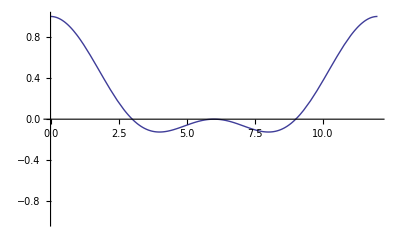

```mathematica
c0[x_]:=2.0*(1.0-Tan[x/4]*Tan[x/4]);
ω=-Pi/3;
H11[x_]:=2.0/(4-2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4]))^2*2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4])
temp1=Plot[H11[t],{t,0,12},PlotRange->{{0,12},{-1,1}}]
```

```mathematica
H11s[x_]:=2.0/(4-2.0*(1.0-Tan[(x*ω+2.0 Pi)/4]*Tan[(x*ω+2.0 Pi)/4]))^2*2.0*(1.0-Tan[(x*ω+2.0 Pi)/4]*Tan[(x*ω+2.0 Pi)/4])
```

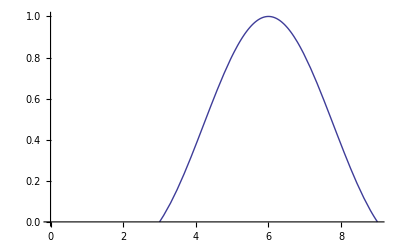

```mathematica
temp2=Plot[H11s[t],{t,0,9},PlotRange->{{0,9},{0,1}}]
```

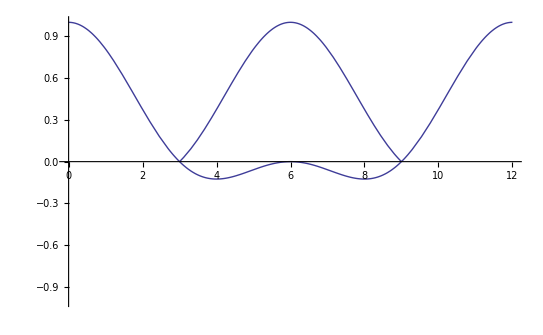

```mathematica
Show[temp1,temp2]
```

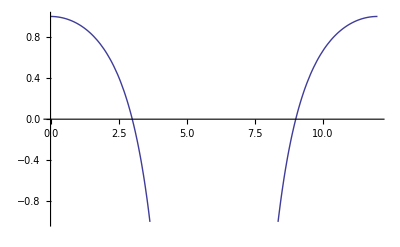

```mathematica
H11inv[x_]:=(1.0-Tan[x*ω/4]*Tan[x*ω/4])
temp3=Plot[H11inv[t],{t,0,12},PlotRange->{{0,12},{-1,1}}]
```

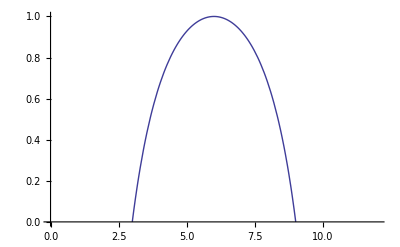

```mathematica
H11invs[x_]:=(1.0-Tan[(x*ω+2.0 Pi)/4]*Tan[(x*ω+2.0 Pi)/4]);
temp4=Plot[H11invs[t],{t,0,12},PlotRange->{{0,12},{0,1}}]
```

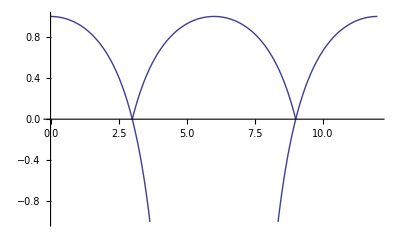

```mathematica
Show[temp3,temp4]
```

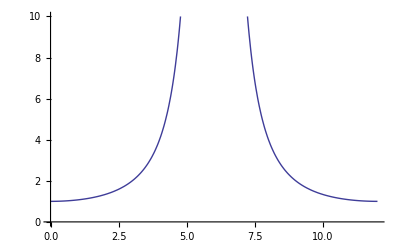

```mathematica
H22inv[x_]:=0.5*(2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4])+0.25*4.0*Tan[x*ω/4]*4.0*Tan[x*ω/4])
temp5=Plot[H22inv[t],{t,0,12},PlotRange->{{0,12},{0,10}}]
```

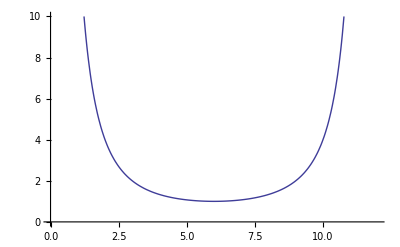

```mathematica
H22invs[x_]:=0.5*(2.0*(1.0-Tan[(x*ω+2.0 Pi)/4]*Tan[(x*ω+2.0 Pi)/4])+0.25*4.0*Tan[(x*ω+2.0 Pi)/4]*4.0*Tan[(x*ω+2.0 Pi)/4])
temp6=Plot[H22invs[t],{t,0,12},PlotRange->{{0,12},{0,10}}]
```

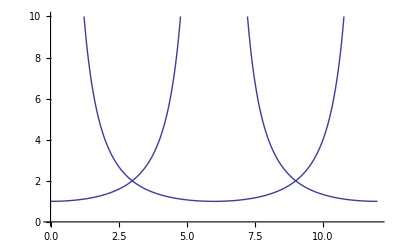

```mathematica
Show[temp5,temp6]
```

-Graphics-

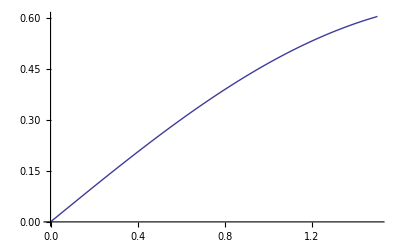

```mathematica
H13[x_]:=2.0/(4-2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4]))^2*4.0*Tan[-x*ω/4];
Plot[H13[t],{t,0,1.5}]
```

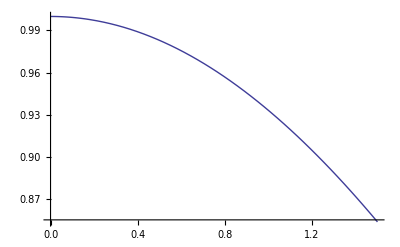

```mathematica
H22[x_]:=2.0/(4-2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4]))^2*(2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4])+4.0*Tan[-x*ω/4]*4.0*Tan[-x*ω/4]/4);
Plot[H22[t],{t,0,1.5}]
```

```mathematica
H31[x_]:=2.0/(4-2.0*(1.0-Tan[x*ω/4]*Tan[x*ω/4]))^2*(-4.0*Tan[-x*ω/4]);
Plot[H31[t],{t,0,1.5}]
```

-Graphics-

```mathematica
ACOS[-1.0]
```

```mathematica
ArcCos[-1.]
```

3.14159